```mathematica
dataX = Import["/Users/yuxinmiao/Documents/文稿 - 于欣淼的MacBook Pro/JI/JI2020Summer/VE401/project2/dataProcessed.csv", "HeaderLines"-> 1];
```

```mathematica
dataAll= Import["/Users/yuxinmiao/Documents/文稿 - 于欣淼的MacBook Pro/JI/JI2020Summer/VE401/project2/term_project_overlay_data.csv", "Dataset"];
```

```mathematica
overlayy = dataAll[All,2]//Normal;
overlayy = Drop[overlayy, 1];
```

```mathematica
modelOy = LinearModelFit[{dataX, overlayy}]
```

FittedModel[0.706481 #1+0.00264355 #2+«10»+0.00265074 #11]

```mathematica
modelOy["BestFit"]
```

0.706481 #1+0.00264355 #2+0.00358417 #3+3.04558×10^-6 #4+5.51767×10^-6 #5-9.48762×10^-6 #6+0.0163108 #7+0.0131395 #8+0.000787553 #9-0.00335037 #10+0.00265074 #11

```mathematica
modelOy["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
modelOy["RSquared"]
```

0.389161

```mathematica
modelOy["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
#1 | 0.706481 | 0.116706 | 6.0535 | 5.44671×10^-9
#2 | 0.00264355 | 0.000534222 | 4.94842 | 1.41241×10^-6
#3 | 0.00358417 | 0.000544968 | 6.57684 | 2.99956×10^-10
#4 | 3.04558×10^-6 | 8.26423×10^-6 | 0.368525 | 0.712808
#5 | 5.51767×10^-6 | 7.61008×10^-6 | 0.725048 | 0.469132
#6 | -9.48762×10^-6 | 7.45802×10^-6 | -1.27214 | 0.204561
#7 | 0.0163108 | 0.00623137 | 2.61753 | 0.00942216
#8 | 0.0131395 | 0.00361407 | 3.63564 | 0.000339551
#9 | 0.000787553 | 0.000545719 | 1.44315 | 0.150289
#10 | -0.00335037 | 0.00122337 | -2.73865 | 0.00663376
#11 | 0.00265074 | 0.000346898 | 7.64126 | 5.18725×10^-13

```mathematica
modelOy["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
#2 | 1 | 7.95436 | 7.95436 | 20.5442 | 9.21372×10^-6
#3 | 1 | 13.0471 | 13.0471 | 33.6975 | 2.03711×10^-8
#4 | 1 | 0.0940583 | 0.0940583 | 0.24293 | 0.62255
#5 | 1 | 0.508758 | 0.508758 | 1.314 | 0.252818
#6 | 1 | 0.753979 | 0.753979 | 1.94735 | 0.164168
#7 | 1 | 2.47212 | 2.47212 | 6.38489 | 0.0121561
#8 | 1 | 5.31795 | 5.31795 | 13.735 | 0.000261604
#9 | 1 | 0.975778 | 0.975778 | 2.5202 | 0.113718
#10 | 1 | 5.22313 | 5.22313 | 13.4901 | 0.000295953
#11 | 1 | 22.6071 | 22.6071 | 58.3889 | 5.18725×10^-13
Error | 239 | 92.5366 | 0.387182 |  | 
Total | 249 | 151.491 |  |  |

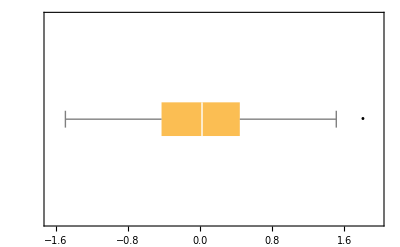

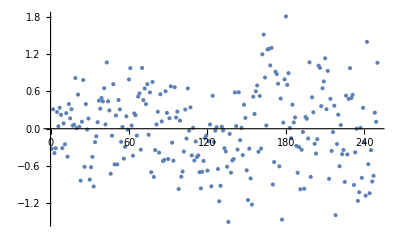

```mathematica
Oyre = modelOy["FitResiduals"];
BoxWhiskerChart[Oyre, "Outliers", BarOrigin->Left]
ListPlot[Oyre]
```

```mathematica
(*The Critical Value*)
InverseCDF[StudentTDistribution[239],1-0.05]
```

1.65125